# 36: Lanczos Iteration

Arnoldi and all sorts of other stuff gets simpler for symmetric matrices. As you would expect Upper Hessenberg matrices become tridiagonal.  One other thing that happens is the general Arnoldi Iteration gets called Lanczos in the special symmetric case. Just as a reminder the Krylov space is 	
	𝒦_n(A,b):=span({b,A.b,A^2.b,…,A^(n-1).b})
and Arnoldi iteratively computes a nested sequence of orthonormal basis for the Krylov space (represented by orthogonal matrices Q_n∈ℝ^(m×n)) and a rectangular Upper Hessenberg matrices H_n∈ℝ^((n+1)×n) which represents the action of A on these basis through
	A.Q_n=Q_(n+1).H_n=Q_n.H_n[1:n,1:n]+H_n[n+1,n] q_(n+1). 
The question is what simplifies when A is real symmetric.  We are going to look at the Arnoldi code and work out what can be tidied up.

```mathematica
Arnoldi[A_][{Q_,H_}]:= Module[{m,n,HNew,w,h,q},
{m,n}=Dimensions[Q];
HNew=ConstantArray[0,{n+1,n}];HNew⟦1;;n,1;;n-1⟧=H;
w=A.Q⟦All,n⟧;
Do[
q=Q⟦All,k⟧;
HNew⟦k,n⟧=q.w;
w=w-HNew⟦k,n⟧ q,
{k,1,n}];
HNew⟦n+1,n⟧=Norm[w];
w=w/HNew⟦n+1,n⟧;
{ArrayFlatten[({{Q, {w}ᵀ}})],HNew}
]
```

Not surprisingly the Hessenberg matrix becomes tridiagonal.  This is because

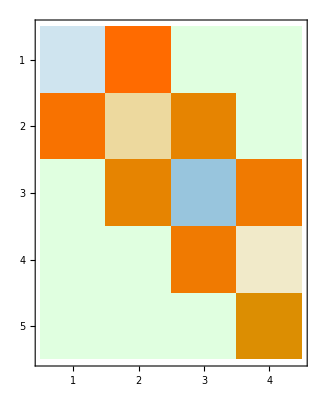

```mathematica
m=123;
A=RandomReal[{-1,1},{m,m}]; A= A + Aᵀ;
b=Normalize[RandomReal[{-1,1},m]];
{Q0,H0}={{b}ᵀ,{{}}};
{Q1,H1}=Arnoldi[A][{Q0,H0}];
{Q2,H2}=Arnoldi[A][{Q1,H1}];
{Q3,H3}=Arnoldi[A][{Q2,H2}];
{Q4,H4}=Arnoldi[A][{Q3,H3}];
MatrixPlot[Chop[H4],ColorRules->{0->LightGreen}]
```